```mathematica
aMatrix={{0,1,0},{980,0,-2.8},{0,0,-100}};
bMatrix={{0},{0},{100}};
cMatrix={{1,0,0}};
```

```mathematica
poles=Eigenvalues[aMatrix]
```

{-100.,-31.305,31.305}

```mathematica
x0={0.01,0,0};
```

```mathematica
sys=StateSpaceModel[{aMatrix,bMatrix,cMatrix}]
```

01009800-2.8000-100100000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
y=OutputResponse[{sys,x0},{0},t]
```

{ ⅇ^(-131.305 t) (-1.61915×10^-20 ⅇ^(31.305 t)+0.005 ⅇ^(100. t)+0.005 ⅇ^(162.61 t))}

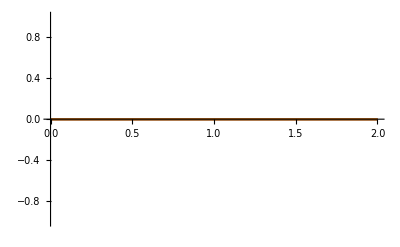

```mathematica
Plot[Evaluate@{u,y},{t,0,2}]
```